```mathematica
(*M=50;e=0.45;
a[i_]:=(1-(2i/M-1)^2)/2;
A=Table[Switch[i-j,-1,e,0,1-e-a[i],1,a[i],_,0],{i,0,M},{j,0,M}];
A[[M+1,M+1]]=1;
pinit=ConstantArray[0,M+1];pinit[[M/2+1]]=1;*)
```

```mathematica
timebetweenenvchanges=180;
M=Floor[(r-μ)/s]+1;
lambdas=Table[1/timebetweenenvchanges,{i,0,M-1}];
mus=Prepend[Table[( 2Log[ K/r(r-μ-i s)s]-Log[ s/(U i)])s/(Log[s/(U i)])^2,{i,1,M-1}],0];
A=ConstantArray[0,{M,M}];
For[i=2,i≤  M-1,i++,
A[[i]][[i-1]]=mus[[i]];
A[[i]][[i]]=1-lambdas[[i]]-mus[[i]];
A[[i]][[i+1]]=lambdas[[i]]];
A[[1]][[1]]=1-lambdas[[1]]; A[[1]][[2]]=lambdas[[1]];  
A[[M]][[M]]=1;
```

```mathematica
pinit=ConstantArray[0,M];pinit[[20]]=1;
dists=Table[pinit.MatrixPower[A,n],{n,1,10000,100}];
ListPlot3D[dists,PlotRange-> Full]
```

-Graphics3D-

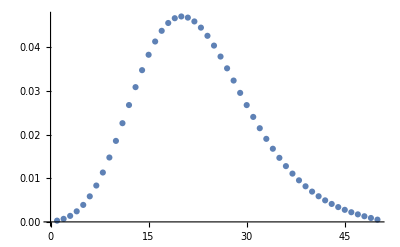

```mathematica
(*Quasistationary distribution*)
piatt[t_]:=pinit.MatrixPower[A,t];
t=100000;
qs=piatt[t][[;;-2]]/(1-piatt[t][[M]]);
extprobgrowth=(1-piatt[t+1][[M]])/(1-piatt[t][[M]]);
ListPlot[qs]
```

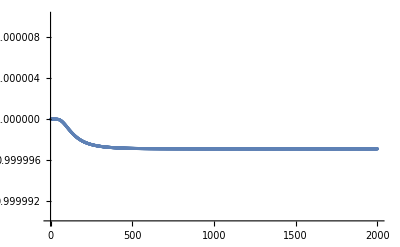

```mathematica
ListPlot[Table[(1-piatt[t+1][[M]])/(1-piatt[t][[M]]),{t,100,200000,100}],PlotRange-> {0.99999,1.00001}]
```

```mathematica
(*reverse time transition matrix*)
B=Table[Append[Table[qs[[j]]A[[j,i]]/(qs[[i]] extprobgrowth),{j,1,M-1}],0],{i,1,M-1}];
B=Append[B,ConstantArray[0,M]]; B[[M,M-1]]=1;
```

```mathematica
pext=Append[ConstantArray[0,M-1],1];
dists=Table[pext.MatrixPower[B,n],{n,1,60000,1}];
(*ListPlot3D[dists,PlotRange-> Full]*)
```

```mathematica
meanireversetime=Table[Sum[(j-1) dists[[i,j]],{j,1,M}],{i,1,Length[dists]}];
sigmaireversetime=Table[Sqrt[Sum[(j-1-meanireversetime[[i]])^2 dists[[i,j]],{j,1,M}]],{i,1,Length[dists]}];
```

```mathematica
Export["/home/jbertram/repos/popgenextinction/code/beforeexttheory.csv",{meanireversetime,sigmaireversetime},"Data"];
```

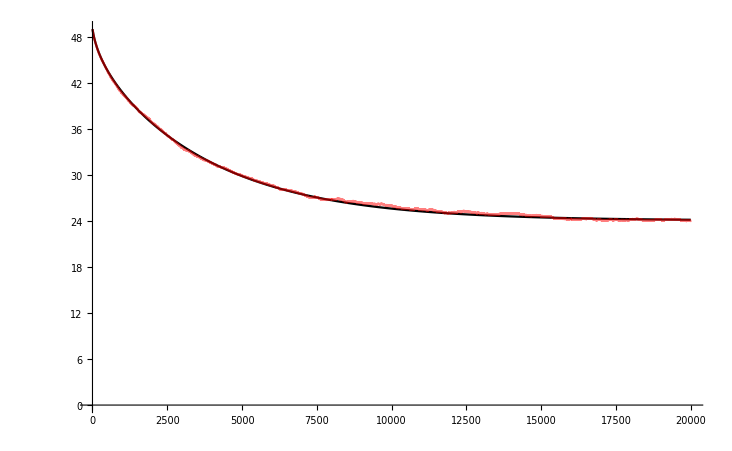

```mathematica
ListLinePlot[{meanireversetime,Mean[beforeextinction]-1},PlotStyle-> {Black,{Red,Opacity[0.5]}}]
```